```mathematica
Propagacja polarytonu przy użyciu rozkładu na fale płaskie
(d EE)/(d R)= -OD/L V(r) EE+ (4L)/OD(1 + (Ω/Γ)^2 V(r))(d^2 EE)/(d r^2)
EE = Subscript[Σ, n=-l]^l Subscript[c, n] e^(i k r n)
```

```mathematica
1/(1-2I(r/rb)^6) (*efektywny potencjał, rb - promień blokady rydbergowskiej*)
Vk=FourierTransform[%, r, dk,Assumptions->{ rb∈Reals && rb > 0}]
```

1/(1-(2 ⅈ r^6)/rb^6)

((1/6+ⅈ/6) √π rb ((-ⅈ √2 ⅇ^(((1-ⅈ) dk rb)/2^(2/3))+(2 √2 ⅇ^(((-1)^(1/12) dk rb)/2^(1/6)))/(ⅈ+√3)+(1-ⅈ) (-1)^(5/12) ⅇ^(((-1)^(5/12) dk rb)/2^(1/6))) HeavisideTheta[-dk]+(-ⅈ √2 ⅇ^(-((1-ⅈ) dk rb)/2^(2/3))+(2 √2 ⅇ^(-((-1)^(1/12) dk rb)/2^(1/6)))/(ⅈ+√3)+(1-ⅈ) (-1)^(5/12) ⅇ^(-((-1)^(5/12) dk rb)/2^(1/6))) HeavisideTheta[dk]))/2^(2/3)

```mathematica
-OD/L V[r]+(4 L)/OD(1+(Ω/Γ)^2 V[r])(-n^2 k^2) (*po obłożeniu przez Vk (z dk=(n-m)k), współczynnik macierzowy m, n*) 
{c0,cV}=Coefficient[%,V[r],{0,1}] (*wkład od c0 będzie miał w macierzy tylko część diagonalną, cV jedną i drugą*)
```

-(OD V[r])/L-(4 k^2 L n^2 (1+(Ω^2 V[r])/Γ^2))/OD

{-(4 k^2 L n^2)/OD,-OD/L-(4 k^2 L n^2 Ω^2)/(OD Γ^2)}

```mathematica
l =11; (*rozmiar macierzy*)

A = Array[#&, l, {-(l - 1) / 2,(l - 1) / 2}];
V2[m_,n_] = cV Vk;
V3[m_,n_] = V2[m, n]/.dk->(n-m) k ;
V4[n_]=c0+Limit[V2[m,n], dk->0];
M1 = Outer[V3, A, A];
M2 = Outer[V4, A];
M= M1 -DiagonalMatrix[Diagonal[M1]]+ DiagonalMatrix[M2]; (*musimy odjąć i dodać część diagonalną od cV Vk, bo trzeba dla niej osobno policzyć granice przy funkcji theta dążącej do 0*)
MatrixForm[M]
```

(1)
 |  |  |  |

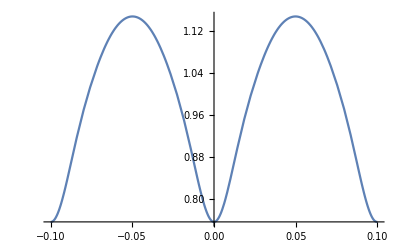

```mathematica
(*Wektor własny odpowiadający maksymalnej wartości własnej dla danego k*)
k0 = 63;
Mnum = M/.{OD->500,L->1,Ω->0,Γ->1,k->k0,rb->0.01};
MatrixForm[Mnum];
{lambda, v} = Eigensystem[Mnum];
v[[Position[Re[lambda],Max[Re[lambda]]][[1]][[1]]]];
Sum[%[[i+(l+1)/2]]  Exp[I i k0 r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}];
Plot[Abs[%],{r,-0.1,0.1}]
```

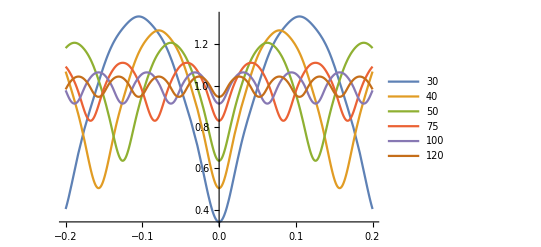

```mathematica
(*Porównanie wektora własnego odpowiadającego maksymalnej wartości własnej dla róznych k*)
M/.{OD->500,L->1,Ω->0,Γ->1,rb->0.01};
Table[{lambda, v} = Eigensystem[%/.k->kv];
vmax = v[[Position[Re[lambda],Max[Re[lambda]]][[1]][[1]]]];
{Abs@Sum[vmax[[i+(l+1)/2]]  Exp[I i kv r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}],kv},
{kv,{30,40,50,75,100,120}}
];
#1&@@@%;
Plot[%,{r,-0.2,0.2}, PlotRange->All,PlotLegends->(#2&@@@%%)]
```

```mathematica
(*Pełna symulacja*)
kv = 20;
M/.{OD->500,L->1,Ω->0,Γ->1,rb->0.01,k->kv};
v = MatrixExp[% R].Normal@SparseArray[(l+1)/2->1,{l}];
Sum[v[[i+(l+1)/2]]  Exp[I i kv r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}];
Manipulate[Plot[Re[%],{r, -0.2,0.2}],{R,0,1, 0.01}]
```

```mathematica
(*Pełna symulacja w jednym miejscu*)
l =41;

A = Array[#&, l, {-(l - 1) / 2,(l - 1) / 2}];
V2[m_,n_] = cV Vk;
V3[m_,n_] = V2[m, n]/.dk->(n-m) k ;
V4[n_]=c0+Limit[V2[m,n], dk->0];
M1 = Outer[V3, A, A];
M2 = Outer[V4, A];
M= M1 -DiagonalMatrix[Diagonal[M1]]+ DiagonalMatrix[M2];
MatrixForm[M];
kv = 3;
M/.{OD->500,L->1,Ω->0.45,Γ->1,rb->0.01,k->kv};
v = MatrixExp[% t].Normal@SparseArray[(l+1)/2->1,{l}];
Sum[v[[i+(l+1)/2]]  Exp[I i kv r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}];
Manipulate[Plot[Re[%],{r, -1,1}, PlotRange->All],{t,0,10, 0.1}]
```

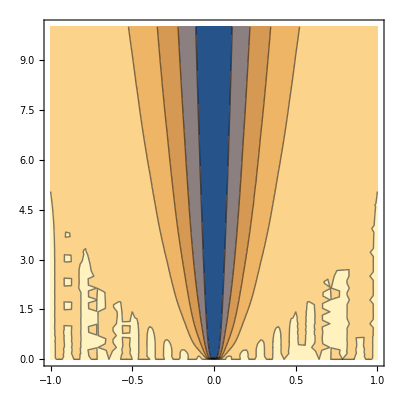

```mathematica
Sum[v[[i+(l+1)/2]]  Exp[I i kv r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}];
(*Export["ryd.mtx", Abs[%]^2, "MTX"]*)
ContourPlot[Re[%],{r, -1,1},{t,0,10}]
```

```mathematica
%63
```

97+ⅇ^(60 ⅈ r) ((-0.000526688+0.0000106433 ⅈ) ((0.+0. ⅈ)+(0.894071-0.0593865 ⅈ) (ⅇ^(-0.0183418 t) Cos[0.0000663082 t]-ⅈ ⅇ^(-0.0183418 t) Sin[0.0000663082 t]))+53+(0.167296-0.0343547 ⅈ) ((0.+0. ⅈ)+(0.146088+21 ⅈ) (1)))
 |  |  |  |

```mathematica
Sum[v[[i+(l+1)/2]]  Exp[I i kv r], {i,Range[-(l - 1) / 2,(l - 1) / 2]}];
Table[%,{r, -1,1, 0.001},{t,0,6, 0.1}]
```

General::munfl: (0.147853-0.0180144 ⅈ) (1.11799×10^-307-2.12434×10^-307 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.147894-0.0180465 ⅈ) (1.11799×10^-307-2.12434×10^-307 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1.-4.82696×10^-17 ⅈ,1.00586-0.000411567 ⅈ,1.00348-0.000296109 ⅈ,1.00273-0.000241081 ⅈ,1.00233-0.000208497 ⅈ,1.00206-0.000186381 ⅈ,1.00188-0.0001701 ⅈ,1.00173-0.000157465 ⅈ,1.00161-0.000147288 ⅈ,1.00152-0.000138862 ⅈ,1.00144-0.000131736 ⅈ,1.00137-0.000125606 ⅈ,1.00131-0.00012026 ⅈ,1.00126-0.000115544 ⅈ,34,1.0002-0.0000714197 ⅈ,1.00013-0.0000723145 ⅈ,1.00004-0.0000733568 ⅈ,0.999953-0.0000745492 ⅈ,0.999854-0.0000758942 ⅈ,0.999746-0.0000773938 ⅈ,0.999629-0.0000790497 ⅈ,0.999503-0.0000808633 ⅈ,0.999367-0.0000828357 ⅈ,0.999221-0.0000849676 ⅈ,0.999064-0.0000872597 ⅈ,0.998896-0.0000897119 ⅈ,0.998717-0.0000923243 ⅈ},1999,{1}}
 |  |  |  |

```mathematica
Export["rydberg.mtx", %, "MTX"]
```

Export::type: $Failed cannot be exported to the MatrixMarket format.

$Failed